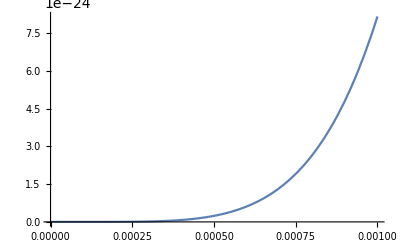

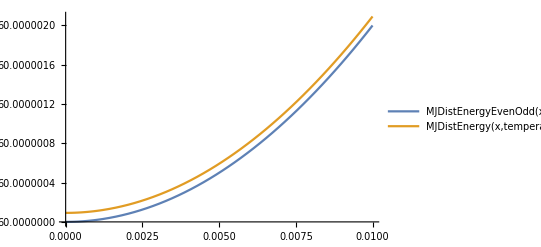

```mathematica
ClearAll[c, k, WP, MJDist, MJDistEnergy, MJDistEnergyEvenOdd, restenergy, temperature, relativisticFlux, dimensions]
c := 299792458
k := 1
WP := 10

MJDist[E_, Ez_, T_, flux_, d_] := ((flux*Sqrt[Pi])/(c*Ez^d*BesselK[(d + 1)/2, Ez/(k*T)]*Gamma[d/2]))*(Ez/(2*k*T))^((d - 1)/2)*E*
    (E^2 - Ez^2)^((d - 2)/2)*Exp[-E/(k*T)]; 

MJDistEnergy[Ez_, T_, flux_, d_] := NIntegrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}, WorkingPrecision -> WP]

MJDistEnergyEvenOdd[Ez_, T_, flux_, dd_] := 
  Limit[-((Ez^(1/2 - d/2)*flux*Pi*(1/(k*T))^(1/2 - d/2)*(Ez/(k*T))^((1/2)*(-1 + d))*
      (-2*k*T*BesselI[(1/2)*(-1 - d), Ez/(k*T)]*Gamma[1 + d/2] + (Ez*BesselI[(1 - d)/2, Ez/(k*T)] - 
         k*T*BesselI[(1 + d)/2, Ez/(k*T)] - Ez*BesselI[(3 + d)/2, Ez/(k*T)])*Gamma[d/2])*Sec[(d*Pi)/2])/
     (2*c*BesselK[(1 + d)/2, Ez/(k*T)]*Gamma[d/2])), {d -> dd}]

restenergy := 0.0001
temperature := 10
relativisticFlux := 299792458
dimensions := 6
Plot[MJDist[x, restenergy, temperature, relativisticFlux, dimensions], {x, 0, 0.001}]
Plot[{MJDistEnergyEvenOdd[x, temperature, relativisticFlux, dimensions], MJDistEnergy[x, temperature, relativisticFlux, 
    dimensions]}, {x, 0, 0.01}, PlotLegends -> "Expressions"]
```

```mathematica
ClearAll[c, k, WP, MJDistEnergy, MJDistEnergyEvenOdd, restenergy, temperature, relativisticFlux, dimensions]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->3]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->5]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->7]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->9]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->13]
Limit[Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}], d->dim]
```

ConditionalExpression[(flux (-Ez BesselI[1,Ez/(k T)] PolyGamma[0,3/2]+k T BesselI[2,Ez/(k T)] PolyGamma[0,3/2]+Ez BesselI[3,Ez/(k T)] PolyGamma[0,3/2]+3 k T BesselI[2,Ez/(k T)] PolyGamma[0,5/2]-3 k T BesselI^(1,0)[-2,Ez/(k T)]+Ez BesselI^(1,0)[-1,Ez/(k T)]+k T BesselI^(1,0)[2,Ez/(k T)]+Ez BesselI^(1,0)[3,Ez/(k T)]))/(2 c BesselK[2,Ez/(k T)]),Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0]

ConditionalExpression[(flux (Ez BesselI[2,Ez/(k T)] PolyGamma[0,5/2]-k T BesselI[3,Ez/(k T)] PolyGamma[0,5/2]-Ez BesselI[4,Ez/(k T)] PolyGamma[0,5/2]-5 k T BesselI[3,Ez/(k T)] PolyGamma[0,7/2]+5 k T BesselI^(1,0)[-3,Ez/(k T)]-Ez BesselI^(1,0)[-2,Ez/(k T)]-k T BesselI^(1,0)[3,Ez/(k T)]-Ez BesselI^(1,0)[4,Ez/(k T)]))/(2 c BesselK[3,Ez/(k T)]),Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0]

ConditionalExpression[(flux (-Ez BesselI[3,Ez/(k T)] PolyGamma[0,7/2]+k T BesselI[4,Ez/(k T)] PolyGamma[0,7/2]+Ez BesselI[5,Ez/(k T)] PolyGamma[0,7/2]+7 k T BesselI[4,Ez/(k T)] PolyGamma[0,9/2]-7 k T BesselI^(1,0)[-4,Ez/(k T)]+Ez BesselI^(1,0)[-3,Ez/(k T)]+k T BesselI^(1,0)[4,Ez/(k T)]+Ez BesselI^(1,0)[5,Ez/(k T)]))/(2 c BesselK[4,Ez/(k T)]),Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0]

ConditionalExpression[(flux (Ez BesselI[4,Ez/(k T)] PolyGamma[0,9/2]-k T BesselI[5,Ez/(k T)] PolyGamma[0,9/2]-Ez BesselI[6,Ez/(k T)] PolyGamma[0,9/2]-9 k T BesselI[5,Ez/(k T)] PolyGamma[0,11/2]+9 k T BesselI^(1,0)[-5,Ez/(k T)]-Ez BesselI^(1,0)[-4,Ez/(k T)]-k T BesselI^(1,0)[5,Ez/(k T)]-Ez BesselI^(1,0)[6,Ez/(k T)]))/(2 c BesselK[5,Ez/(k T)]),Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0]

ConditionalExpression[(flux (Ez BesselI[6,Ez/(k T)] PolyGamma[0,13/2]-k T BesselI[7,Ez/(k T)] PolyGamma[0,13/2]-Ez BesselI[8,Ez/(k T)] PolyGamma[0,13/2]-13 k T BesselI[7,Ez/(k T)] PolyGamma[0,15/2]+13 k T BesselI^(1,0)[-7,Ez/(k T)]-Ez BesselI^(1,0)[-6,Ez/(k T)]-k T BesselI^(1,0)[7,Ez/(k T)]-Ez BesselI^(1,0)[8,Ez/(k T)]))/(2 c BesselK[7,Ez/(k T)]),Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0]

ConditionalExpression[(flux π (2 k T BesselI[1/2 (-1-dim),Ez/(k T)] Gamma[1+dim/2]+(-Ez BesselI[(1-dim)/2,Ez/(k T)]+k T BesselI[(1+dim)/2,Ez/(k T)]+Ez BesselI[(3+dim)/2,Ez/(k T)]) Gamma[dim/2]) Sec[(dim π)/2])/(2 c BesselK[(1+dim)/2,Ez/(k T)] Gamma[dim/2]),(1+dim)/2∉ℤ&&Re[Ez]>0&&Im[Ez]==0&&Re[1/(k T)]>0&&Re[dim]>0]

```mathematica
Integrate[argE MJDist[argE, Ez, T, flux, d], {argE, Ez, Infinity}]
```

ConditionalExpression[-(2^(1/2+1/2 (-3+d)-d/2) Ez^(-d+(1+d)/2) flux π (1/(k T))^(1/2-d/2) (Ez/(k T))^(1/2 (-1+d)) (-2 k T BesselI[1/2 (-1-d),Ez/(k T)] Gamma[1+d/2]+(Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)]) Gamma[d/2]) Sec[(d π)/2])/(c BesselK[(1+d)/2,Ez/(k T)] Gamma[d/2]),Re[Ez]>0&&Im[Ez]==0&&Re[d]>0&&Re[1/(k T)]>0]

```mathematica
-(2^(1/2+1/2 (-3+d)-d/2) Ez^(-d+(1+d)/2) flux π (1/(k T))^(1/2-d/2) (Ez/(k T))^(1/2 (-1+d)) (-2 k T BesselI[1/2 (-1-d),Ez/(k T)] Gamma[1+d/2]+(Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)]) Gamma[d/2]) Sec[(d π)/2])/(c BesselK[(1+d)/2,Ez/(k T)] Gamma[d/2])
```

-(2^(1/2+1/2 (-3+d)-d/2) Ez^(-d+(1+d)/2) flux π (1/(k T))^(1/2-d/2) (Ez/(k T))^(1/2 (-1+d)) (-2 k T BesselI[1/2 (-1-d),Ez/(k T)] Gamma[1+d/2]+(Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)]) Gamma[d/2]) Sec[(d π)/2])/(c BesselK[(1+d)/2,Ez/(k T)] Gamma[d/2])

```mathematica
Simplify[%157]
```

```mathematica
-(flux π (-2 k T BesselI[1/2 (-1-d),Ez/(k T)] (d/2)+(Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)])) Sec[(d π)/2])/(2 c BesselK[(1+d)/2,Ez/(k T)])
```

-(flux π (-d k T BesselI[1/2 (-1-d),Ez/(k T)]+Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)]) Sec[(d π)/2])/(2 c BesselK[(1+d)/2,Ez/(k T)])

```mathematica
Simplify[-(flux π (-d k T BesselI[1/2 (-1-d),Ez/(k T)]+Ez BesselI[(1-d)/2,Ez/(k T)]-k T BesselI[(1+d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)]) Sec[(d π)/2])/(2 c BesselK[(1+d)/2,Ez/(k T)])]
```

```mathematica
(flux π (k T (d BesselI[1/2 (-1-d),Ez/(k T)]+BesselI[(1+d)/2,Ez/(k T)])-Ez( BesselI[(1-d)/2,Ez/(k T)]-Ez BesselI[(3+d)/2,Ez/(k T)])) Sec[(d π)/2])/(2 c BesselK[(1+d)/2,Ez/(k T)])
```

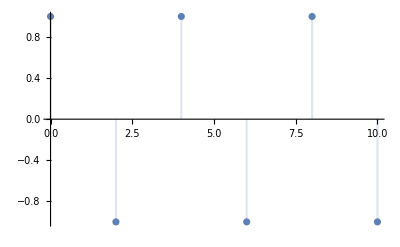

```mathematica
DiscretePlot[Sec[Pi*d/2], {d, 0, 10, 2}]
```

```mathematica
1/(2 c BesselK[5,Ez/(k T)])flux ((-1)^((d-1)/2)Ez BesselI[4,Ez/(k T)] PolyGamma[0,9/2]-(-1)^((d-1)/2)k T BesselI[5,Ez/(k T)] PolyGamma[0,9/2]-(-1)^((d-1)/2)Ez BesselI[6,Ez/(k T)] PolyGamma[0,9/2]-(-1)^((d-1)/2)9 k T BesselI[5,Ez/(k T)] PolyGamma[0,11/2]+(-1)^((d-1)/2)9 k T Derivative[1,0][BesselI][-5,Ez/(k T)]-(-1)^((d-1)/2)Ez Derivative[1,0][BesselI][-4,Ez/(k T)]-(-1)^((d-1)/2)k T Derivative[1,0][BesselI][5,Ez/(k T)]-(-1)^((d-1)/2)Ez Derivative[1,0][BesselI][6,Ez/(k T)])
```

(flux (ⅈ^(-1+d) Ez BesselI[4,Ez/(k T)] PolyGamma[0,9/2]-ⅈ^(-1+d) k T BesselI[5,Ez/(k T)] PolyGamma[0,9/2]-ⅈ^(-1+d) Ez BesselI[6,Ez/(k T)] PolyGamma[0,9/2]-9 ⅈ^(-1+d) k T BesselI[5,Ez/(k T)] PolyGamma[0,11/2]+9 ⅈ^(-1+d) k T BesselI^(1,0)[-5,Ez/(k T)]-ⅈ^(-1+d) Ez BesselI^(1,0)[-4,Ez/(k T)]-ⅈ^(-1+d) k T BesselI^(1,0)[5,Ez/(k T)]-ⅈ^(-1+d) Ez BesselI^(1,0)[6,Ez/(k T)]))/(2 c BesselK[5,Ez/(k T)])

```mathematica
Simplify[%162]
```

```mathematica
-(ⅈ ⅈ^d flux (Ez BesselI[(d-1)/2,Ez/(k T)] PolyGamma[0,d/2]-k T BesselI[(d+1)/2,Ez/(k T)] PolyGamma[0,d/2]-Ez BesselI[(d+3)/2,Ez/(k T)] PolyGamma[0,d/2]-d k T BesselI[(d+1)/2,Ez/(k T)] PolyGamma[0,(d+1)/2]+d k T Derivative[1,0][BesselI][-(d+1)/2,Ez/(k T)]-Ez Derivative[1,0][BesselI][-(d-1)/2,Ez/(k T)]-k T Derivative[1,0][BesselI][(d+1)/2,Ez/(k T)]-Ez Derivative[1,0][BesselI][(d+3)/2,Ez/(k T)]))/(2 c BesselK[(d+1)/2,Ez/(k T)])
```

-(ⅈ ⅈ^d flux (Ez BesselI[1/2 (-1+d),Ez/(k T)] PolyGamma[0,d/2]-k T BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,d/2]-Ez BesselI[(3+d)/2,Ez/(k T)] PolyGamma[0,d/2]-d k T BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,(1+d)/2]+d k T BesselI^(1,0)[1/2 (-1-d),Ez/(k T)]-Ez BesselI^(1,0)[(1-d)/2,Ez/(k T)]-k T BesselI^(1,0)[(1+d)/2,Ez/(k T)]-Ez BesselI^(1,0)[(3+d)/2,Ez/(k T)]))/(2 c BesselK[(1+d)/2,Ez/(k T)])

```mathematica
Simplify[%164]
```

```mathematica
-(ⅈ ⅈ^d flux (Ez (BesselI[1/2 (-1+d),Ez/(k T)] PolyGamma[0,d/2]-BesselI[(3+d)/2,Ez/(k T)] PolyGamma[0,d/2]-Derivative[1,0][BesselI][(1-d)/2,Ez/(k T)]-Derivative[1,0][BesselI][(3+d)/2,Ez/(k T)])-k T (BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,d/2]-d BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,(1+d)/2]+d Derivative[1,0][BesselI][-(1+d)/2,Ez/(k T)]-Derivative[1,0][BesselI][(1+d)/2,Ez/(k T)])))/(2 c BesselK[(1+d)/2,Ez/(k T)])
```

-(ⅈ ⅈ^d flux (-k T (BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,d/2]-d BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,(1+d)/2]+d BesselI^(1,0)[1/2 (-1-d),Ez/(k T)]-BesselI^(1,0)[(1+d)/2,Ez/(k T)])+Ez (BesselI[1/2 (-1+d),Ez/(k T)] PolyGamma[0,d/2]-BesselI[(3+d)/2,Ez/(k T)] PolyGamma[0,d/2]-BesselI^(1,0)[(1-d)/2,Ez/(k T)]-BesselI^(1,0)[(3+d)/2,Ez/(k T)])))/(2 c BesselK[(1+d)/2,Ez/(k T)])

```mathematica
Simplify[%166]
```

(ⅈ ⅈ^d flux (-Ez BesselI[1/2 (-1+d),Ez/(k T)] PolyGamma[0,d/2]+k T BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,d/2]+Ez BesselI[(3+d)/2,Ez/(k T)] PolyGamma[0,d/2]-d k T BesselI[(1+d)/2,Ez/(k T)] PolyGamma[0,(1+d)/2]+d k T BesselI^(1,0)[1/2 (-1-d),Ez/(k T)]+Ez BesselI^(1,0)[(1-d)/2,Ez/(k T)]-k T BesselI^(1,0)[(1+d)/2,Ez/(k T)]+Ez BesselI^(1,0)[(3+d)/2,Ez/(k T)]))/(2 c BesselK[(1+d)/2,Ez/(k T)])